```mathematica
<<EDCRGTCcode.m
```

SetDelayed::write: Tag Laplacian in x_ is Protected.

```mathematica
$Assumptions={t≥0};
```

```mathematica
simpRules=TrigRules;
xCoord={t,x,y,z};
gIN={{-1,0,0,0},{0,a[t]^2,0,0},{0,0,a[t]^2,0},{0,0,0,a[t]^2}};
```

```mathematica
a[t_]=a0[t]+δ a1[t];
```

```mathematica
a0[t_]=a0c*t^(1/2);
```

```mathematica
RGtensors[gIN,xCoord]
```

gdd = (-1 | 0 | 0 | 0
0 | (a0c √t+δ a1[t])^2 | 0 | 0
0 | 0 | (a0c √t+δ a1[t])^2 | 0
0 | 0 | 0 | (a0c √t+δ a1[t])^2)

LineElement = -d[t]^2+(a0c √t+δ a1[t])^2 d[x]^2+(a0c √t+δ a1[t])^2 d[y]^2+(a0c √t+δ a1[t])^2 d[z]^2

gUU = (-1 | 0 | 0 | 0
0 | 1/(a0c √t+δ a1[t])^2 | 0 | 0
0 | 0 | 1/(a0c √t+δ a1[t])^2 | 0
0 | 0 | 0 | 1/(a0c √t+δ a1[t])^2)

gUU computed in 0.008063 sec

Gamma computed in 0.006769 sec

Riemann(dddd) computed in 0.012473 sec

Riemann(Uddd) computed in 0.007504 sec

Ricci computed in 0.006538 sec

Weyl computed in 0.012397 sec

Conformally Flat

Einstein computed in 0.005725 sec

All tasks completed in 0.063223 seconds

```mathematica
RUU=Raise[Rdd,{1,2}]//FullSimplify;
RUUUU=Raise[Rdddd,{1,2,3,4}]//FullSimplify;
```

```mathematica
RddddSq=Contract[Outer[Times,Rdddd,RUUUU],{1,5},{2,6},{3,7},{4,8}]//Simplify;
```

```mathematica
RddSq=Contract[Outer[Times,Rdd,RUU],{1,3},{2,4}]//FullSimplify;
```

```mathematica
RSq=R^2//FullSimplify;
```

```mathematica
P4=(c-ac)/(48 π^2)RddddSq+(2 ac-c)/(24 π^2)RddSq+(c-3 ac)/(144 π^2)RSq//FullSimplify;
```

```mathematica
uU={1,0,0,0};
ud=Lower[uU,1];
```

```mathematica
Δdd=Outer[Times,ud,ud]+gdd;
ΔUU=Raise[Δdd,{1,2}]//Simplify;
```

```mathematica
Tdd=ϵ[t] Outer[Times,ud,ud]+P[t] Δdd+δ*P4 Δdd//Simplify;
TUU=Raise[Tdd,{1,2}]//Simplify;
```

```mathematica
ϵ[t_]=3*P0[t]+3*δ P1[t];
P[t_]=P0[t]+δ P1[t];
```

```mathematica
Contract[Outer[Times,gUU,Tdd],{1,3},{2,4}]/.δ->0//Simplify
```

0

```mathematica
EIN=Rdd-1/2 gdd R+δ Λ gdd-8 π GN Tdd//Simplify;
CONS=Contract[covD[TUU,{1,2}],{1,3}]//Simplify;
```

```mathematica
EIN0=EIN/.δ->0//Simplify;
CONS0=CONS/.δ->0//Simplify;
```

```mathematica
EIN1=Coefficient[Series[EIN,{δ,0,1}]//Simplify//Normal,δ]//Simplify;
CONS1=Coefficient[Series[CONS,{δ,0,1}]//Simplify//Normal,δ]//Simplify;
```

```mathematica
P0[t_]=1/(32 GN π t^2);
```

```mathematica
EIN0
CONS0
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{0,0,0,0}

## First order

```mathematica
EQS1=Join[DeleteDuplicates[Table[EIN1[[ii,ii]],{ii,1,4}]],{CONS1[[1]]}]//Simplify;
```

```mathematica
EQS1//MatrixForm
```

(-(2 a0c Λ+(3 a1[t])/t^(5/2)+48 a0c GN π P1[t]-(6 a1'[t])/t^(3/2))/(2 a0c)
-8 a0c^2 GN π t P1[t]+(a0c (-(a0c ac GN)/π+4 a0c t^4 Λ-4 t^(5/2) a1'[t]-8 t^(7/2) a1''[t]))/(4 t^3)
(3 (a0c ac GN-4 π t^(3/2) a1[t]+128 a0c GN π^2 t^4 P1[t]+8 π t^(5/2) a1'[t]+64 a0c GN π^2 t^5 P1'[t]))/(64 a0c GN π^2 t^5))

```mathematica
Flatten[Solve[{EQS1[[1]]==0},P1[t]]//Simplify]
```

{P1[t]→-(2 a0c Λ+(3 a1[t])/t^(5/2)-(6 a1'[t])/t^(3/2))/(48 a0c GN π)}

```mathematica
P1[t_]=-(2 a0c Λ+(3 a1[t])/t^(5/2)-(6 a1'[t])/t^(3/2))/(48 a0c GN π);
```

```mathematica
DSolve[0==((EQS1//Simplify)[[2]]),a1[t],t]//FullSimplify//Flatten
```

{a1[t]→(a0c (-9 ac GN+16 π t^4 Λ)+72 π t ((1+t) C[1]+ⅈ (-1+t) C[2]))/(144 π t^(3/2))}

```mathematica
(*P1rule=Flatten[Solve[{EQS1[[2]]==0},P1[t]]//Simplify]*)
```

```mathematica
(*EQS1/.P1rule//Simplify//Expand//MatrixForm*)
```

```mathematica
(*E1rule=Solve[0==(EQS1[[1]]/.P1rule//Simplify),ϵ1[t]]//Simplify//Flatten*)
```

```mathematica
(*E1Prule={ϵ1'[t]->D[-(2 Λ+(3 a1[t])/t^(5/2)-(6 a1'[t])/t^(3/2))/(16 GN π),t]}*)
```

```mathematica
a1[t_]=(a0c (-9 ac GN+16 π t^4 Λ)+72 π t ((1+t) C[1]+ⅈ (-1+t) C[2]))/(144 π t^(3/2));
```

```mathematica
EIN1//Simplify
CONS1//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{0,0,0,0}

```mathematica
Series[gdd,{δ,0,1}]/.C[2]->0/.C[1]->0//Simplify
```

{{-1,0,0,0},{0,a0c^2 t+(a0c^2 (-(9 ac GN)/π+16 t^4 Λ) δ)/(72 t)+O[δ]^2,0,0},{0,0,a0c^2 t+(a0c^2 (-(9 ac GN)/π+16 t^4 Λ) δ)/(72 t)+O[δ]^2,0},{0,0,0,a0c^2 t+(a0c^2 (-(9 ac GN)/π+16 t^4 Λ) δ)/(72 t)+O[δ]^2}}

```mathematica
Series[a[t],{δ,0,1}]/.C[2]->0/.C[1]->0//Simplify
```

√t+(-(ac GN)/(16 π t^(3/2))+1/9 t^(5/2) Λ) δ+O[δ]^2

```mathematica
Series[Tdd,{δ,0,1}]/.C[2]->0/.C[1]->0//Simplify
```

{{3/(32 GN π t^2)+(((9 ac)/t^4-(8 π Λ)/GN) δ)/(192 π^2)+O[δ]^2,0,0,0},{0,1/(32 GN π t)+((99 ac GN-16 π t^4 Λ) δ)/(2304 GN π^2 t^3)+O[δ]^2,0,0},{0,0,1/(32 GN π t)+((99 ac GN-16 π t^4 Λ) δ)/(2304 GN π^2 t^3)+O[δ]^2,0},{0,0,0,1/(32 GN π t)+((99 ac GN-16 π t^4 Λ) δ)/(2304 GN π^2 t^3)+O[δ]^2}}

## Check solutions

```mathematica
<<EDCRGTCcode.m
```

SetDelayed::write: Tag Laplacian in x_ is Protected.

```mathematica
$Assumptions={t≥0};
simpRules=TrigRules;
xCoord={t,x,y,z};
gIN={{-1,0,0,0},{0,a[t]^2,0,0},{0,0,a[t]^2,0},{0,0,0,a[t]^2}};
a[t_]=a0[t]+δ a1[t];
a0[t_]=a0c*t^(1/2);
RGtensors[gIN,xCoord];
```

gdd = (-1 | 0 | 0 | 0
0 | (a0c √t+δ a1[t])^2 | 0 | 0
0 | 0 | (a0c √t+δ a1[t])^2 | 0
0 | 0 | 0 | (a0c √t+δ a1[t])^2)

LineElement = -d[t]^2+(a0c √t+δ a1[t])^2 d[x]^2+(a0c √t+δ a1[t])^2 d[y]^2+(a0c √t+δ a1[t])^2 d[z]^2

gUU = (-1 | 0 | 0 | 0
0 | 1/(a0c √t+δ a1[t])^2 | 0 | 0
0 | 0 | 1/(a0c √t+δ a1[t])^2 | 0
0 | 0 | 0 | 1/(a0c √t+δ a1[t])^2)

gUU computed in 0.006483 sec

Gamma computed in 0.006655 sec

Riemann(dddd) computed in 0.009322 sec

Riemann(Uddd) computed in 0.009979 sec

Ricci computed in 0.008808 sec

Weyl computed in 0.012462 sec

Conformally Flat

Einstein computed in 0.005929 sec

All tasks completed in 0.064623 seconds

```mathematica
RUU=Raise[Rdd,{1,2}]//FullSimplify;
RUUUU=Raise[Rdddd,{1,2,3,4}]//FullSimplify;
RddddSq=Contract[Outer[Times,Rdddd,RUUUU],{1,5},{2,6},{3,7},{4,8}]//Simplify;
RddSq=Contract[Outer[Times,Rdd,RUU],{1,3},{2,4}]//FullSimplify;
RSq=R^2//FullSimplify;
P4=(c-ac)/(48 π^2)RddddSq+(2 ac-c)/(24 π^2)RddSq+(c-3 ac)/(144 π^2)RSq//FullSimplify;
uU={1,0,0,0};
ud=Lower[uU,1];
Δdd=Outer[Times,ud,ud]+gdd;
ΔUU=Raise[Δdd,{1,2}]//Simplify;
Tdd=ϵ[t] Outer[Times,ud,ud]+P[t] Δdd+δ*P4 Δdd//Simplify;
TUU=Raise[Tdd,{1,2}]//Simplify;
ϵ[t_]=3*P0[t]+3*δ P1[t];
P[t_]=P0[t]+δ P1[t];
```

```mathematica
P0[t_]=1/(32 GN π t^2);
a1[t_]=(a0c (-9 ac GN+16 π t^4 Λ)+72 π t ((1+t) C1+ⅈ (-1+t) C3))/(144 π t^(3/2));
C3=I C2;
P1[t_]=-(2 a0c Λ+(3 a1[t])/t^(5/2)-(6 a1'[t])/t^(3/2))/(48 a0c GN π);
```

```mathematica
a1[t]//FullSimplify
```

(72 π t (C1+C2+C1 t-C2 t)+a0c (-9 ac GN+16 π t^4 Λ))/(144 π t^(3/2))

```mathematica
EIN=Rdd-1/2 gdd R+δ Λ gdd-8 π GN Tdd//Simplify;
CONS=Contract[covD[TUU,{1,2}],{1,3}]//Simplify;
```

```mathematica
EIN1=Series[EIN,{δ,0,1}]//Simplify
CONS1=Series[CONS,{δ,0,1}]//Simplify
```

{{O[δ]^2,0,0,0},{0,O[δ]^2,0,0},{0,0,O[δ]^2,0},{0,0,0,O[δ]^2}}

{O[δ]^2,0,0,0}

```mathematica
Coefficient[P[t],δ]//FullSimplify
```

(-36 (C1+C2) π t+a0c (9 ac GN-8 π t^4 Λ))/(576 a0c GN π^2 t^4)

```mathematica
a1[t]//FullSimplify
```

(72 π t (C1+C2+C1 t-C2 t)+a0c (-9 ac GN+16 π t^4 Λ))/(144 π t^(3/2))

```mathematica
P[t]/.C1->0/.C2->0/.Λ->0/.δ->1//FullSimplify
```

(ac GN+2 π t^2)/(64 GN π^2 t^4)

```mathematica
a1[t]/.C1->0/.C2->0/.Λ->0//FullSimplify
```

-(a0c ac GN)/(16 π t^(3/2))

```mathematica
Series[gdd,{δ,0,1}]//Simplify
Series[TUU,{δ,0,1}]//Simplify
```

{{-1,0,0,0},{0,a0c^2 t+a0c (ⅈ C2 (-1+t)-(a0c ac GN)/(8 π t)+C1 (1+t)+2/9 a0c t^3 Λ) δ+O[δ]^2,0,0},{0,0,a0c^2 t+a0c (ⅈ C2 (-1+t)-(a0c ac GN)/(8 π t)+C1 (1+t)+2/9 a0c t^3 Λ) δ+O[δ]^2,0},{0,0,0,a0c^2 t+a0c (ⅈ C2 (-1+t)-(a0c ac GN)/(8 π t)+C1 (1+t)+2/9 a0c t^3 Λ) δ+O[δ]^2}}

{{3/(32 GN π t^2)+((9 a0c ac GN-36 C1 π t+36 ⅈ C2 π t-8 a0c π t^4 Λ) δ)/(192 a0c GN π^2 t^4)+O[δ]^2,0,0,0},{0,1/(32 a0c^2 GN π t^3)+((-24 π t (ⅈ C2 (-3+t)+C1 (3+t))+a0c (39 ac GN-16 π t^4 Λ)) δ)/(768 a0c^3 GN π^2 t^5)+O[δ]^2,0,0},{0,0,1/(32 a0c^2 GN π t^3)+((-24 π t (ⅈ C2 (-3+t)+C1 (3+t))+a0c (39 ac GN-16 π t^4 Λ)) δ)/(768 a0c^3 GN π^2 t^5)+O[δ]^2,0},{0,0,0,1/(32 a0c^2 GN π t^3)+((-24 π t (ⅈ C2 (-3+t)+C1 (3+t))+a0c (39 ac GN-16 π t^4 Λ)) δ)/(768 a0c^3 GN π^2 t^5)+O[δ]^2}}

```mathematica
a[t]/.C1->0/.C2->0/.δ->1/.ac->a/.Λ->0//Simplify
```

-(a GN)/(16 π t^(3/2))+√t

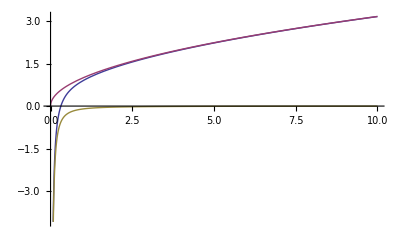

```mathematica
Plot[{√t-0.1/t^(3/2),√t,-0.1/t^(3/2)},{t,0,10}]
```

```mathematica
Series[Contract[Outer[Times,gUU,Tdd],{1,3},{2,4}]//Simplify,{δ,0,1}]-3*δ*P4
```

O[δ]^2

## Check for κ corrections

```mathematica
RBRUU=1/2(Contract[Outer[Times,ΔUU,ΔUU,Rdd],{2,5},{4,6}]+Contract[Outer[Times,ΔUU,ΔUU,Rdd],{2,6},{4,5}])-1/3 Contract[Outer[Times,ΔUU,ΔUU,Rdd],{3,5},{4,6}]//FullSimplify;
```

```mathematica
RUddU=Raise[Rdddd,{1,4}]//FullSimplify;
```

```mathematica
RBRUUUU=1/2(Contract[Outer[Times,ΔUU,ΔUU,RUddU],{2,6},{4,7}]+Contract[Outer[Times,ΔUU,ΔUU,RUddU],{2,7},{4,6}])-1/3 Contract[Outer[Times,ΔUU,ΔUU,RUddU],{3,6},{4,7}]//FullSimplify;
```

```mathematica
κ(RBRUU-2 Contract[Outer[Times,ud,RBRUUUU,ud],{1,2},{5,6}])
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

The are 0, great!

```mathematica
Rtestdd=Contract[Outer[Times,Rdddd,RUUUU],{1,5},{2,6},];
```

```mathematica
Rtestdd=Contract[RUddd,{1,4}]*R;
```

```mathematica
1/2(Contract[Outer[Times,ΔUU,ΔUU,Rtestdd],{2,5},{4,6}]+Contract[Outer[Times,ΔUU,ΔUU,Rtestdd],{2,6},{4,5}])-1/3 Contract[Outer[Times,ΔUU,ΔUU,Rtestdd],{3,5},{4,6}]//FullSimplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

## The metric is conformally flat. Does that mean that t^ab=0?

## Non-perturbatively

```mathematica
<<EDCRGTCcode.m
```

SetDelayed::write: Tag Laplacian in x_ is Protected.

```mathematica
$Assumptions={t≥0};
```

```mathematica
simpRules=TrigRules;
xCoord={t,x,y,z};
gIN={{-1,0,0,0},{0,a[t]^2,0,0},{0,0,a[t]^2,0},{0,0,0,a[t]^2}};
```

```mathematica
RGtensors[gIN,xCoord]
```

gdd = (-1 | 0 | 0 | 0
0 | a[t]^2 | 0 | 0
0 | 0 | a[t]^2 | 0
0 | 0 | 0 | a[t]^2)

LineElement = -d[t]^2+a[t]^2 d[x]^2+a[t]^2 d[y]^2+a[t]^2 d[z]^2

gUU = (-1 | 0 | 0 | 0
0 | 1/a[t]^2 | 0 | 0
0 | 0 | 1/a[t]^2 | 0
0 | 0 | 0 | 1/a[t]^2)

gUU computed in 0.001018 sec

Gamma computed in 0.002285 sec

Riemann(dddd) computed in 0.003167 sec

Riemann(Uddd) computed in 0.002731 sec

Ricci computed in 0.000751 sec

Weyl computed in 0.004842 sec

Conformally Flat

Einstein computed in 0.000843 sec

All tasks completed in 0.019661 seconds

```mathematica
RUU=Raise[Rdd,{1,2}]//FullSimplify;
RUUUU=Raise[Rdddd,{1,2,3,4}]//FullSimplify;
```

```mathematica
RddddSq=Contract[Outer[Times,Rdddd,RUUUU],{1,5},{2,6},{3,7},{4,8}]//Simplify;
```

```mathematica
RddSq=Contract[Outer[Times,Rdd,RUU],{1,3},{2,4}]//FullSimplify;
```

```mathematica
RSq=R^2//FullSimplify;
```

```mathematica
P4=(c-ac)/(48 π^2)RddddSq+(2 ac-c)/(24 π^2)RddSq+(c-3 ac)/(144 π^2)RSq//FullSimplify;
```

```mathematica
uU={1,0,0,0};
ud=Lower[uU,1];
```

```mathematica
Δdd=Outer[Times,ud,ud]+gdd;
ΔUU=Raise[Δdd,{1,2}]//Simplify;
```

```mathematica
Tdd=ϵ[t] Outer[Times,ud,ud]+P[t] Δdd+P4 Δdd//Simplify;
TUU=Raise[Tdd,{1,2}]//Simplify;
```

```mathematica
ϵ[t_]=3*P0[t]+δ ϵ1[t];
P[t_]=P0[t]+δ P1[t];
```

```mathematica
Contract[Outer[Times,gUU,Tdd],{1,3},{2,4}]//Simplify
```

3 P[t]-ϵ[t]-(3 ac a'[t]^2 a''[t])/(2 π^2 a[t]^3)

```mathematica
EIN=Rdd-1/2 gdd R+δ Λ gdd-8 π GN Tdd//Simplify;
CONS=Contract[covD[TUU,{1,2}],{1,3}]//Simplify;
```

```mathematica
EIN0=EIN/.δ->0//Simplify;
CONS0=CONS/.δ->0//Simplify;
```

```mathematica
EIN1=Coefficient[Series[EIN,{δ,0,1}]//Simplify//Normal,δ]//Simplify;
CONS1=Coefficient[Series[CONS,{δ,0,1}]//Simplify//Normal,δ]//Simplify;
```

```mathematica
P0[t_]=1/(32 GN π t^2);
```

```mathematica
EIN0
CONS0
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{0,0,0,0}